```mathematica
Mixing
```

## DEFINE PARAMTERS

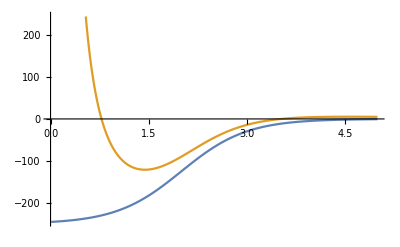

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=250;R=2;a=0.5;μ=8/9 Subscript[m, N];
E2=3;
rmax=5.;dr=0.01;
rlist=Range[dr,rmax,dr];
len=Length[rlist];
Vwoods[r_]:=-V0/(1+Exp[(r-R)/a]);
Vcent[r_,l_]:=(l(l+1)ℏc^2)/(2μ r^2);
V00[r_]:=Vwoods[r]+Vcent[r,0];
V22[r_]:=Vwoods[r]+Vcent[r,2];
V00mat=DiagonalMatrix[V00[rlist]];
V22mat=DiagonalMatrix[V22[rlist]];
ListLinePlot[{V00[rlist],V22[rlist]},DataRange->{dr,rmax}]
```

```mathematica
(*MIXING*)
V02mat=V20mat=DiagonalMatrix[1/1000 Vwoods[rlist]];
```

```mathematica
(*INITIAL HAMILTONIAN*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H000:=V00mat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1]);
H022:=V22mat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1])+E2;
H0:=ArrayFlatten[{{H000,V02mat},{V20mat,H022}}];
```

## BOUND SOLUTIONS

```mathematica
(*BOUND SOLUTION*)
κ0[En_]:=Sqrt[(2μ Abs[En])/ℏc^2];
κ2[En_]:=Sqrt[(2μ Abs[En+E2])/ℏc^2];
wavebound0[En_,r_]:=SphericalHankelH1[0,I κ0[En] r];
wavebound2[En_,r_]:=SphericalHankelH1[2,I κ2[En] r];
Bbound0[En_]:=rmax/wavebound0[En,rmax](D[wavebound0[En,r],r]/.r->rmax);
Bbound2[En_]:=rmax/wavebound2[En,rmax](D[wavebound2[En,r],r]/.r->rmax);
(*HAMILTONIAN*)
Hnewbound[En_]:=Module[{H=H0},H[[len,len]]=V00mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bbound0[En]/rmax-1);H[[2 len,2 len]]=V22mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bbound2[En]/rmax-1);H];
(*RETURNS EIGENVALUE*)
eigenvbound[{En_,i_}]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnewbound[En]]],First];{eval[[i]],i})
```

```mathematica
ϵ=10^-10;
n=1;
evals=List[];evecs=List[];
```

```mathematica
(*RETURNS EIGENSYSTEM*)
En=NestWhileList[eigenvbound,{-V0/2,n},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,10][[-1,1]];
While[Re[En]<0,
evals=Append[evals,En];
evecs=Append[evecs,evec[[n]]];n++;En=NestWhileList[eigenvbound,{-V0/2,n},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,10][[-1,1]];]
```

```mathematica
(*MATCHES AMPLITUDE & PLOTS*)
constbound[i_]:=(evecs[[i,-len-1]]+evecs[[i,-1]])/Abs[wavebound0[evals[[i]],rmax]+wavebound2[evals[[i]],rmax]];
rmaxx=10.;
Manipulate[ListLinePlot[{Transpose[{rlist,Part[evecs⟦i⟧,1;;len]+Part[evecs⟦i⟧,len+1;;2 len]}],Transpose[{Range[rmax,rmaxx,dr],constbound[i](Abs[wavebound0[evals[[i]],Range[rmax,rmaxx,dr]]+wavebound2[evals[[i]],Range[rmax,rmaxx,dr]]])}]},PlotRange->All],{i,1,Length[evals],1}]
```

```mathematica
(*Manipulate[ListLinePlot[Transpose[{rlist,Part[evecs⟦i⟧,1;;len]}],PlotRange->All],{i,1,Length[evals],1}]*)
```

```mathematica
(*Manipulate[ListLinePlot[Transpose[{rlist,Part[evecs⟦i⟧,len+1;;2 len]}],PlotRange->All],{i,1,Length[evals],1}]*)
```

```mathematica
(*Manipulate[ListLinePlot[Transpose[{rlist,Part[evecs⟦i⟧,1;;len]+Part[evecs⟦i⟧,len+1;;2 len]}],PlotRange->All],{i,1,Length[evals],1}]*)
```

## RESONANCE STATES

```mathematica
(*RESONANCE SOLUTION*)
k0[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
k2[En_?NumericQ]:=Sqrt[(2μ (En-E2))/ℏc^2];
waveres0[En_?NumericQ,r_]:=SphericalHankelH1[0,k0[En] r];
waveres2[En_?NumericQ,r_]:=SphericalHankelH1[2,k2[En] r];
Bres0[En_?NumericQ]:=rmax/waveres0[En,rmax](D[waveres0[En,r],r]/.r->rmax);
Bres2[En_?NumericQ]:=rmax/waveres2[En,rmax](D[waveres2[En,r],r]/.r->rmax);
(*HAMILTONIAN*)
Hnewres[En_?NumericQ]:=Module[{H=H0},H[[len,len]]=V00mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bres0[En]/rmax-1);H[[2 len,2 len]]=V22mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bres2[En]/rmax-1);H];
(*RETURNS EIGENVALUE*)
eigenvres[{En_?NumericQ,i_}]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnewres[En]]],First];{eval[[i]],i})
(*eigenvres1[En_?NumericQ,i_,l_]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnewres[En,l]]],First];eval[[i]])*)
```

```mathematica
ϵ=10^-10;
n=5;
evals=List[];evecs=List[];
```

```mathematica
(*RETURNS EIGENSYSTEM*)
(*En=x/.FindRoot[Im[eigenvres1[x,n,l]]==Im[x],{x,0.1+0.I,0.,V0}]//Timing*)
En=NestWhileList[eigenvres,{0,n},Abs[Abs[#1[[1]]]-Abs[#2[[1]]]]>ϵ&,2,10][[-1,1]];
evals=Append[evals,En];
evecs=Append[evecs,evec[[n]]];
```

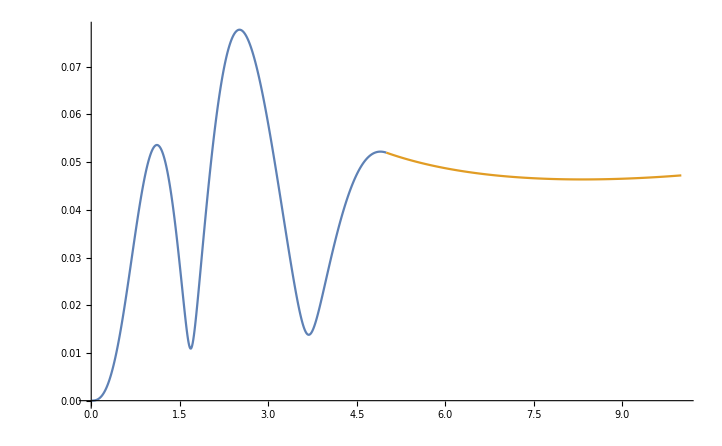

```mathematica
(*MATCHES AMPLITUDE & PLOTS*)
constres[i_]:=(evecs[[i,-len-1]]+evecs[[i,-1]])/(Abs[waveres0[evals[[i]],rmax]]+Abs[waveres2[evals[[i]],rmax]]);
rmaxx=10.;
ListLinePlot[{Transpose[{rlist,Abs[Part[evecs⟦1⟧,1;;len]+Part[evecs⟦1⟧,len+1;;2 len]]}],Transpose[{Range[rmax,rmaxx,dr],Abs[constres[1]](Abs[waveres0[evals[[1]],Range[rmax,rmaxx,dr]]]+Abs[waveres2[evals[[1]],Range[rmax,rmaxx,dr]]])}]},PlotRange->All]
```

```mathematica
evals
```

{34.6831-6.70266 ⅈ}

```mathematica
(*ListLinePlot[Transpose[{rlist,Abs[Part[evecs⟦1⟧,1;;len]]}],PlotRange->All]*)
```

```mathematica
(*ListLinePlot[Transpose[{rlist,Abs[Part[evecs⟦1⟧,len+1;;2 len]]}],PlotRange->All]*)
```

```mathematica
(*ListLinePlot[Transpose[{rlist,Abs[Part[evecs⟦1⟧,1;;len]+Part[evecs⟦1⟧,len+1;;2 len]]}],PlotRange->All]*)
```

## SCATTERING SOLUTIONS

```mathematica
(*SCATTERING SOLUTION*)
k0[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
k2[En_?NumericQ]:=Sqrt[(2μ (En-E2))/ℏc^2];
wavescat0[En_,r_,δ_]:=1/2 Exp[I δ](Cos[δ]SphericalBesselJ[0,k0[En] r]-Sin[δ] SphericalBesselY[0,k0[En] r]);
wavescat2[En_,r_,δ_]:=1/2 Exp[I δ](Cos[δ]SphericalBesselJ[2,k2[En] r]-Sin[δ] SphericalBesselY[2,k2[En] r]);
(*Bscat[En_?NumericQ,δ_?NumericQ,l_]:=k[En] rmax(((Cos[δ] ∂_x SphericalBesselJ[l,x]/.x->k[En] rmax)-(Sin[δ] ∂_x SphericalBesselY[l,x]/.x->k[En] rmax))/(Cos[δ]SphericalBesselJ[l,k[En] rmax]-Sin[δ]SphericalBesselY[l,k[En] rmax]));*)
Bscat0[En_?NumericQ,δ_?NumericQ]:=rmax/wavescat0[En,rmax,δ] D[wavescat0[En,r,δ],r]/.{r->rmax};
Bscat2[En_?NumericQ,δ_?NumericQ]:=rmax/wavescat2[En,rmax,δ] D[wavescat2[En,r,δ],r]/.{r->rmax};
(*HAMILTONIAN*)
Hnewscat[En_?NumericQ,δ_?NumericQ]:=Module[{H=H0},H[[len,len]]=V00mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bscat0[En,δ]/rmax-1);H[[2 len,2 len]]=V22mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr Bscat2[En,δ]/rmax-1);H];
(*RETURNS EIGEINVALUE*)
eigenvscat[En_?NumericQ,i_,δ_?NumericQ]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnewscat[En,δ]]],First];eval[[i]]);
(*FINDS ENERGY LEVEL AND PHASE*)
(*findnd[En_]:=Module[{phase=List[],n=1},(While[Max[Table[eigenvscat[{En,n,δ,l}][[1]],{δ,0.,π,0.01}]]<En,n++;];phase=Table[{eigenvscat[{En,n,δ,l}][[1]],δ},{δ,0,π,0.001}];δ=phase[[Position[phase[[All,1]],Nearest[phase[[All,1]],En][[1]]][[1,1]],2]];{n,δ})]*)
findnd[En_?NumericQ]:=Module[{n=1},While[Max[Table[eigenvscat[En,n,x],{x,0.,π,0.1}]]<En,n++;];δ=x/.FindRoot[eigenvscat[En,n,x]==En,{x,0.,-Pi,Pi}];If[δ<0,δ=π+δ];{n,δ}];
(*MATCHES AMPLITUDE AND PLOTS*)
constscat[i_]:=(evec[[i,-len-1]]+evec[[i,-1]])/(wavescat0[eval[[i]],rmax,δ]+wavescat2[eval[[i]],rmax,δ]);
wvplot[En_]:=Module[{n=findnd[En][[1]],δ=findnd[En][[2]]},{eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnewscat[En,δ]]],First];Print[{En,eval[[n]],n,δ}];ListLinePlot[{Transpose[{rlist,Abs[Part[evec⟦n⟧,1;;len]+Part[evec⟦n⟧,len+1;;2 len]]}],Transpose[{Range[rmax,rmaxx,dr],Abs[constscat[n] (wavescat0[eval[[n]],Range[rmax,rmaxx,dr],δ]+wavescat2[eval[[n]],Range[rmax,rmaxx,dr],δ])]}]},PlotRange->All]]
```

```mathematica
vals[En_]:=Module[{n=findnd[En][[1]],δ=findnd[En][[2]]},{eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnewscat[En,δ]]],First];Print[{En,eval[[n]],n,δ}];]
```

```mathematica
(*vals[7.49]//Timing*)
```

{34.683,34.683+0. ⅈ,5,1.88327+0. ⅈ}

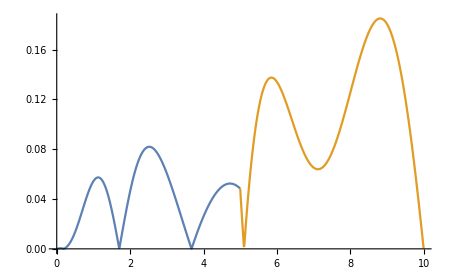
{452.556,-Graphics-}

```mathematica
rmaxx=10.;
wvplot[34.683]//Timing
```

```mathematica
(evec[[5,-len-1]]+evec[[5,-1]])/Abs[(wavescat0[eval[[5]],rmax,1.8832661380900455]+wavescat2[eval[[5]],rmax,1.8832661380900455])]
```

20.9043+0. ⅈ

```mathematica
Abs[(evec[[5,-len-1]]+evec[[5,-1]])/(wavescat0[eval[[5]],rmax,1.8832661380900455]+wavescat2[eval[[5]],rmax,1.8832661380900455])]
```

20.9043

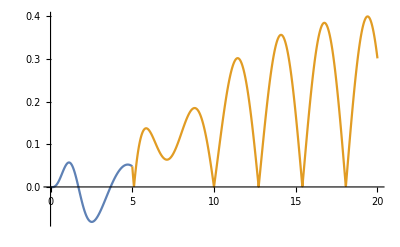

```mathematica
ListLinePlot[{Transpose[{rlist,Part[evec⟦5⟧,1;;len]+Part[evec⟦5⟧,len+1;;2 len]}],Transpose[{Range[rmax,20,dr],Abs[constscat[5] (wavescat0[eval[[5]],Range[rmax,20,dr],1.8832661380900455]+wavescat2[eval[[5]],Range[rmax,20,dr],1.8832661380900455])]}]},PlotRange->All]
```

```mathematica
constscat[5]
```

6.42617+19.892 ⅈ

```mathematica
(*ListLinePlot[{Transpose[{rlist,Part[evec[[n]],1;;len]}]},PlotRange->All]*)
```

```mathematica
(*ListLinePlot[{Transpose[{rlist,Part[evec[[n]],len+1;;2 len]}]},PlotRange->All]*)
```

```mathematica
(*ListLinePlot[{Transpose[{rlist,Part[evec[[n]],1;;len]+Part[evec[[n]],len+1;;2 len]}]},PlotRange->All]*)
```

```mathematica
phasedata=Table[{x,findnd[x][[2]]},{x,4.5,5.5,0.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

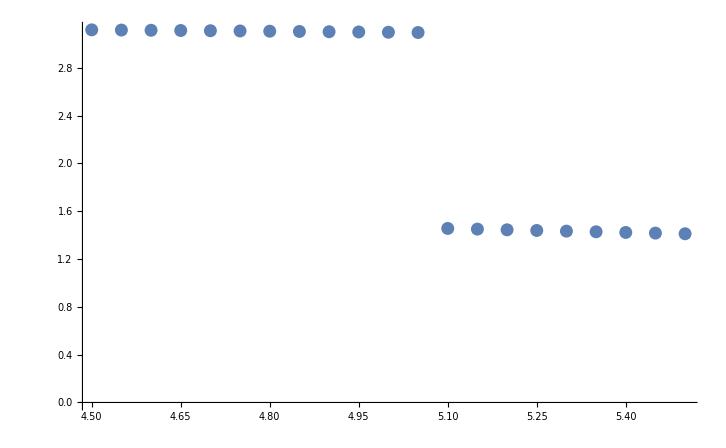

```mathematica
ListPlot[phasedata,GridLines->{None, {{Pi/2,Red}}}]
```

```mathematica
findres[n_]:=(phase[y_?NumericQ]:=Re[FindRoot[eigenvscat[y,n,x,l]==y,{x,0.,-Pi,Pi}][[1,2]]];Subscript[δ, res]=y/.FindRoot[phase[y]==Pi/2,{y,3.2,3.,3.5}])
```

```mathematica
Subscript[δ, res]=findres[2]
```

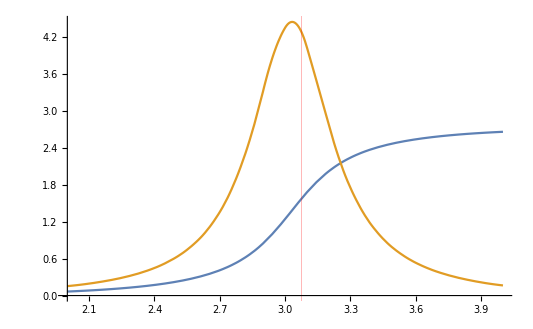

```mathematica
funcphasedata=Interpolation[phasedata,Method->"Spline"];
dfuncphasedata=funcphasedata';
Plot[Evaluate[{funcphasedata[x],dfuncphasedata[x]}],{x,2.0,4.0},GridLines->{{{Subscript[δ, res],Red}},None}]
```

```mathematica
1/(D[funcphasedata[x],x]/.x->findres[1])
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {3.5} is at the edge of the search region {3.,3.5} in coordinate 1 and the computed search direction points outside the region.

1.31784